# Animiranje grafov, vektorji in matrike

## Animiranje grafov

### Subsection. naloga:

Narišite graf funkcije y=a sin (k x+n) tako, da boste lahko vrednosti parametrov a, k in n spreminjali v obsegu od -3 do 3. Območje risanja omejite na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
(* V funkciji Plot uporabite nastavitvi Range->{-5,5} in AspectRatio->Automatic *)
```

```mathematica
f[x_]:=a*Sin[k*x+n]
```

```mathematica
Manipulate[Plot[a*Sin[k*x+n],{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic],{a,-5,5},{k,-5,5},{n,-5,5}]
```

### Subsection. naloga:

Narišite graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0) tako, da boste lahko spreminjali vrednosti parametrov k, n, x_0 in y_0. Na sliki označite z majhnim krogcem, kje leži točka T.
Namig: dva grafa na isti sliki narišete s funkcijo Plot tako, da predpisa podate v seznamu: {f[x], g[x]}.

```mathematica
(* Točko dodate z nastavitvijo Epilog->{PointSize[Large],Point[{{x0,y0}}]}] *)
```

```mathematica
f[x_]:=k*x+n
```

```mathematica
g[x_]:=-1/k x+m
```

```mathematica
Subscript[x, 0]=(n+m)/(k+1/k)
```

(m+n)/(1/k+k)

```mathematica
Subscript[y, 0]=f[Subscript[x, 0]]
```

n+(k (m+n))/(1/k+k)

```mathematica
m=Subscript[y, 0]+1/k Subscript[x, 0]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

n+(TerminatedEvaluation[RecursionLimit]+n)/(k (1/k+k))+(k (TerminatedEvaluation[RecursionLimit]+n))/(1/k+k)

```mathematica
Manipulate[Plot[{k*x+n,-1/k x+a+1/k b},{x,-10,10},PlotRange->{-10,10},AspectRatio->Automatic,Epilog->{PointSize[Large],Point[{{b,a}}]}],{k,-5,5},{n,-5,5},{b,-5,5},{a,-5,5}]
```

### Subsection. naloga:

Definirajte funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter narišite njen graf skupaj s tangento v točki x_0, tako da boste lahko spreminjali vrednosti parametra x_0. Na sliki označite z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
f[x_]:=(x(x-2)^2)/(x^2+1)
```

```mathematica
g[x_]:=k*x+n
```

```mathematica
n=f[a]-f'[a]*a
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{(x(x-2)^2)/(x^2+1),f'[a]*(x-a)+f[a]},{x,-10,10},PlotRange->{-10,10},AspectRatio->Automatic,Epilog->{PointSize[Large],Point[{{a,f[a]}}]}],{a,-10,10}]
```

### Subsection. naloga:

1. Narišite graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]
2. Prikažite, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.
3. Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

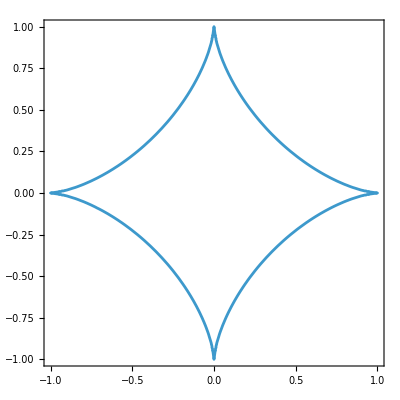

```mathematica
ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1,{x,-1,1},{y,-1,1}]
```

```mathematica
Manipulate[ContourPlot[Abs[x]^p+Abs[y]^p==1,{x,-2,2},{y,-2,2}],{{p,2,"Mulitplier"},0,4}]
```

## Vektorji in matrike

### Subsection. naloga:

1. Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.
2. Izračunaj njun skalarni produkt.
3. Izračunaj njun vektorski produkt.s
4. Kateri od vektorjev je daljši?
5. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
v1={1,2,3}
v2={-3,-2,5}
```

{1,2,3}

{-3,-2,5}

```mathematica
v1.v2
```

8

```mathematica
w=Cross[v1,v2]
```

{16,-14,4}

```mathematica
Norm[v1]
```

√14

```mathematica
Norm[v2]
```

√38

```mathematica
Norm[w]
```

6 √13

```mathematica
Norm[v1]<Norm[v2]<Norm[w]
```

True

### Subsection. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3. S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

### Subsection. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

### Subsection. naloga:

1. Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.
2. Izračunaj njeno determinanto.
3. Izračunaj njene lastne vrednosti.
4. Izračunaj njene lastne vektorje.
5. Ali je matrika diagonalizabilna?
6. Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.
7. Preveri, ali velja pogoj za diagonalizabilnost.